## Intro to Logistic Differential Equations

### The slope field for e^x

```mathematica
VP = VectorPlot[{1,y},{x,-5,5},{y,0,5},Axes->True,GridLines->Automatic];
```

```mathematica
PS = Plot[2Exp[x],{x,-5,5}];
```

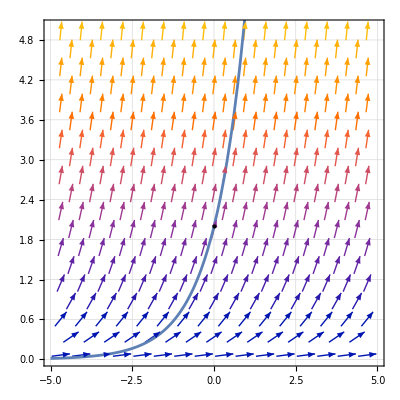

```mathematica
Show[VP,PS,Graphics[{PointSize[Large],Point[{0,2}]}]]
```

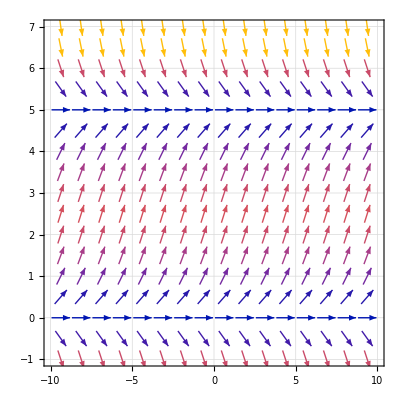

```mathematica
SV=VectorPlot[{1,0.2y(5-y)},{x,-10,10},{y,-1,7},VectorPoints->"Regular",Axes->True,GridLines->Automatic]
```

## Logistics Graph 1

```mathematica
SV=VectorPlot[{1,0.2y(5-y)},{x,-10,10},{y,-1,7},VectorPoints->"Regular",Axes->True,GridLines->Automatic]
```

-Graphics-

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==2},y[t],t][[1]];
SS = Plot[sol,{t,-5,5}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==4},y[t],t][[1]];
SSS = Plot[sol,{t,-5,5}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==0.1},y[t],t][[1]];
SolP = Plot[sol,{t,-5,5}];
```

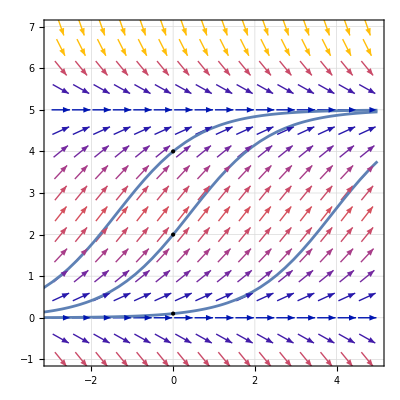

```mathematica
Show[SV,SS,SolP,SSS,Graphics[{PointSize[Large],Point[{0,2}]}],
Graphics[{PointSize[Large],Point[{0,4}]}],
Graphics[{PointSize[Large],Point[{0,0.1}]}]]
```

## Logistics Graph 2

```mathematica
SV=VectorPlot[{1,0.2y(5-y)},{x,-10,10},{y,-1,7},VectorPoints->"Regular",Axes->True,GridLines->Automatic]
```

-Graphics-

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==2},y[t],t][[1]];
SS = Plot[sol,{t,-10,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==4},y[t],t][[1]];
SSS = Plot[sol,{t,-10,10}];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
ClearAll[y]
sol=y[t]/.DSolve[{y'[t]==0.2y[t](5-y[t]),y[0]==0.1},y[t],t][[1]];
SolP = Plot[sol,{t,-10,10}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
SL = Plot[2.5,{x,-10,10},PlotStyle->{Thick,Green}];
```

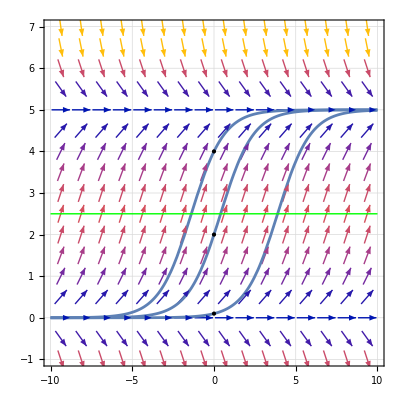

```mathematica
Show[SV,SS,SolP,SSS,SL,Graphics[{PointSize[Large],Point[{0,2}]}],
Graphics[{PointSize[Large],Point[{0,4}]}],
Graphics[{PointSize[Large],Point[{0,0.1}]}]]
```